# Introduction à Mathematica

## UPEC, Paris.

Guillaume Saës (guillaume.saes@u-pec.fr)

## Introduction

### Qu'est-ce-que Mathematica ?

Mathematica est un logiciel de calcul formel et numérique développé par Wolfram Research.
Le calcul formel (CAS en anglais : computer algebra system) permet la manipulation d’expressions mathématiques sous forme symbolique, par exemple : calcul de dérivées, de primitives, simplification d’expressions, etc... 
Le calcul numérique permet l’évaluation d’expressions mathématiques sous forme numérique, par exemple : calcul des premières décimales du nombre π, évaluation approchée d’intégrales, etc...).
Mathematica est un langage de programmation sophistiqué et permet aussi de manipuler des signaux ou images.

### Wolfram Alpha

Wolfram Alpha (www.wolframalpha.com) est un outil en ligne gratuit répondant à toutes sortes de questions (qui doivent être posées en anglais) et qui utilise une grande base de donnée et des calculs Mathematica. Il permet d’accéder avec un simple navigateur internet à beaucoup de fonctionnalités de Mathematica. Par exemple, la demande “derivative of sin(x)” (dérivée de sin(x)) calcule la réponse “cos(x)” et donne au passage d’autres informations utiles (propriétés de la fonction, courbes, développements limités, etc...).

## Débuter en Mathematica

### Interface graphique

L’interface graphique de Mathematica s’occupe de l’interaction entre l’utilisateur et le noyau (“Kernel”) du logiciel qui va interpréter les instructions d’entrée. L’interface gère le fichier de travail (“Notebook”) et permet de taper des instructions et de visualiser les résultats. De plus, il dispose d’un traitement de texte permettant ainsi d’inclure du texte parmi les calculs.

### Un fichier Mathematica

Un fichier Mathematica est appelé “Notebook” et détient l’extension “.nb”. Il est structuré de cellules (“Cells”). Une cellule est constitué d’une ou de plusieurs lignes et est repérée par un crochet à droite du fichier. On peut avoir des cellules contenant des instructions Mathematica (cellule de type “In”), des résultats de calculs (cellule de type “Out”), du texte (cellule du type “Text”), un titre de paragraphe (cellule de type “Section”), etc ...

Une cellule peut contenir plusieurs sous-cellules, formant ainsi des groupes structurés de cellules. Pour faciliter la lecture du fichier, on peut ouvrir ou fermer des groupes de cellules en double-cliquant sur le crochet correspondant (ou en cliquant sur le triangle à gauche du titre).

Pensez à sauvegarder souvent votre fichier Mathematica (menu “File”, puis “Save” ou “Save As”), les mauvaises manipulations étant fréquentes...

### L’aide Mathematica

Mathematica inclut une documentation exhaustive (voir le menu “Help”, puis “Documentation Center” ou “Virtual Book”), incluant de nombreux exemples directement exécutables dans les pages d’aide.
La commande “Find Selected Function” (ou touche “F1”) est très pratique : dans un fichier Mathematica, après avoir placé le curseur sur une instruction Mathematica, appuyez sur F1 pour afficher la page d’aide correspondante à cette instruction.

A utiliser le plus souvent possible !!

## Les bases sur Mathematica

### Premier calcul en Mathematica

On tape une instruction, puis on l’exécute en maintenant “Maj” (ou “Shift”) et en appuyant sur la touche “Entrée” :

```mathematica
1+2
```

3

La ligne d’instruction est désigné par “In” suivi du numéro de l’instruction et de la ligne de résultat désigné par “Out” suivi du numéro de l’instruction.

### Calculs arithmétiques simples

Voici quelques calculs arithmétiques simples qu’on peut effectuer avec Mathematica :

```mathematica
(3.8-4.1)*0.5^2+1204/257
```

4.60982

Voici l'exemple d'un calcul avec une puissance :

```mathematica
13^21
```

247064529073450392704413

Par défaut, Mathematica simplifie les fractions mais ne donne pas de valeur décimale :

```mathematica
38/12
```

19/6

Pour avoir une valeur décimale approché d'une expression, on peut utiliser la fonction "N" en donnant l'argument entre crochets :

```mathematica
N[38/12]
```

3.16667

On peut aussi faire des calculs avec des nombres complexes, le nombre imaginaire ⅈ étant écrit "I" :

```mathematica
(1-3I)*(2+4I)
```

14-2 ⅈ

Il faut faire attention au type de nombre qu’on utilise (nombre entier, nombre décimal, nombre réel,...).
En effet pour un logiciel de programmation comme Mathematica 100*0.25=25 n’est pas entier.
Vous multipliez un entier et un nombre décimal ce qui vous donne un nombre décimal par défaut.

```mathematica
IntegerQ[25]
```

True

```mathematica
IntegerQ[100*0.25]
```

False

### Définir des variables

Pour définir une variable mathématiques “x” contenant une valeur numérique “5”, on tape :

```mathematica
x=4
```

4

Le signe "=" réalise ce que l'on appelle en informatique une "affectation" (et on dit qu'on affecte à "x" la valeur 5). Dans tous les calculs suivants, Mathematica replacera la variable "x" par sa valeur :

```mathematica
x^2
```

16

La ligne suivante change la valeur de "x" :

```mathematica
x=5+6
```

11

Le nom d'une variable peut être composé de plusieurs lettres et chiffres, par exemple

```mathematica
abc5=78
```

78

mais le nom d'une variable ne peut pas commencer par un chiffre.

On peut taper des équations avec les variables que l'on a définies de la même manière qu'en mathématiques, par exemple :

```mathematica
(2x+abc5)/4
```

25

le signe de la multiplication (*) entre "2" et "x" n'est pas nécessaire.

Pour effacer la valeur numérique d'une variable, on utilise la fonction "Clear" :

```mathematica
Clear[x]
```

On peut vérifier que la variable n'a alors plus de valeur numérique :

```mathematica
x
```

x

### Quelques constantes mathématiques

Mathematica dispose de quelques variables déjà définies (constantes) et prêtes à être utilisées, par exemple :

- le nombre π

```mathematica
Pi
```

π

- le nombre e

```mathematica
E
```

ⅇ

- le nombre imaginaire i

```mathematica
I
```

ⅈ

- l'infini ∞ :

```mathematica
Infinity
```

∞

Rappellons que pour forcer l'affichage d'une valeur décimale approchée, on peut utiliser la fonction "N". Voici les 100 premiers chiffres de π :

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

## Les fonctions sur Mathematica

### Introduction

On peut définir ses propres fonctions en Mathematica. Par exemple, pour définir la fonction f(x) = x^2 , on tape :

```mathematica
f[x_]:=x^2
```

### Structure

Dans la définition d'une fonction, on utilise habituellement le signe ": =" qui signifie une "affectation retardée", c'est-à-dire que le membre de droite n'est pas évalué et affecté à f(x) lors de la définition de la fonction ci-dessus mais il sera évalué plus tard à chaque utilisation de la fonction après substitution de "x" par une valeur. Parfois, on peut vouloir forcer l'évaluation du membre de droite lors de la définition de la fonction et on utilise alors le signe de l'affection "="; mais il faut alors s'assurer que la variable "x" ne contient pas de valeur.

Dans le membre de gauche, l'argument "x" de la fonction est donné entre crochets et doit obligatoirement être suivi d'un tiret bas "_" (ou "underscore"), ce qui informe Mathematica que "x" est une variable muette qui devra être remplacée par l'argument avec lequel la fonction sera appelée.

On peut alors appeler la fonction f avec comme argument "3" par exemple

```mathematica
f[3]
```

9

ou n'importe quelle expression, par exemple "2+4 z"

```mathematica
f[2+4z]
```

(2+4 z)^2

J’insiste sur l’importance du “:=” avec cette exemple :

```mathematica
Clear[f]
x=2;
f[x_]=x^2;
f[3]
```

4

On peut préciser le type de variable à prendre en compte après le “underscore” :

```mathematica
Clear[f]
f[x_Integer]:=x^2
```

```mathematica
f[0.2]
```

f[0.2]

```mathematica
f[4]
```

16

On peut définir des fonctions à plusieurs variables

```mathematica
g[x_,y_]:=x+y/x^2
```

Comme pour les variables, on peut effacer les fonctions qui viennent d'être définies par la fonction "Clear" :

```mathematica
Clear[f]
```

```mathematica
Clear[g]
Clear[x]
```

### Quelques fonctions mathématiques

Mathematica dispose de nombreuses fonctions déjà définies.Voici quelques fonctions mathématiques courantes :

- racine carrée : √x

```mathematica
Sqrt[x]
```

√x

- exponentielle : e^x

```mathematica
Exp[x]
```

ⅇ^x

- logarithme népérien : ln(x)

```mathematica
Log[x]
```

Log[x]

- logarithme en base b : log_b(x)  (le plus souvent, b=10)

```mathematica
Log[b,x]
```

Log[x]/Log[b]

- fonctions trigonométriques :

```mathematica
Sin[x]
```

Sin[x]

```mathematica
Cos[x]
```

Cos[x]

```mathematica
Tan[x]
```

Tan[x]

```mathematica
ArcSin[x]
```

ArcSin[x]

```mathematica
ArcCos[x]
```

ArcCos[x]

```mathematica
ArcTan[x]
```

ArcTan[x]

- valeur absolue : |x|

```mathematica
Abs[x]
```

Abs[x]

- factorielle : n !

```mathematica
n!
```

n!

ou

```mathematica
Factorial[n]
```

n!

A retenir : les fonctions Mathematica déjà définies commencent toujours par une majuscule. Placez le curseur sur une fonction et appuyez sur F1 pour afficher la page d'aide de cette fonction. Si on se demande si Mathematica dispose d'une fonction particulière, ou si on a oublié le nom d'une fonction, le plus simple est de faire une recherche dans l'aide (menu "Help > Documentation Center").

## Exemple de calculs formels et numériques

### Calculs formels

Mathematica dispose de fonctions très puissantes permettant d'effectuer toutes sortes de calculs formels. Quelques exemples :

- simplification de (sin(x))^2+(cos(x))^2

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

- développement de l'expression (2x+3)(x^2-6)

```mathematica
Expand[(2x+3)(x^2-6)]
```

-18-12 x+3 x^2+2 x^3

- factorisation  de l'expression x^2-2x-3

```mathematica
Factor[x^2-2x-3]
```

(-3+x) (1+x)

- calcul de la dérivée de x^n par rapport à x

```mathematica
D[x^n,x]
g'[x]
```

n x^(-1+n)

g'[x]

- calcul d'un primitive de cos(x)

```mathematica
Integrate[Cos[x],x]
```

Sin[x]

- calcul de l'intégrale ∫_0^∞ e^(-x^2)ⅆx

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

- calcul de la limite de (x-1) ln(x-1) quand x→ 1

```mathematica
Limit[Sin[x]/x,x->0]
```

1

- calcul du développement limité de cos(x) autour de x=0   à l'ordre 10

```mathematica
Series[Cos[x],{x,0,10}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+O[x]^11

- Résolution de l'équation x^2-3 x +2 = 0 en l'inconnue x

```mathematica
Solve[x^2-3x+2==0,x]
```

{{x→1},{x→2}}

On obtient deux solutions réelles. Notez que pour définir une équation, on utilise le signe "= =" pour ne pas confondre avec le signe d'affectation "=".

Ces fonctions disposent en général d'un grand nombre d'options permettant de faire face à des cas particuliers ou difficiles. Consultez les pages d'aide de ces fonctions.

### Calculs numériques

Parfois, un calcul formel n'est pas faisable, et il faut alors faire un calcul numérique approché. Quelques exemples :

- calcul d'une valeur approchée de l'intégrale ∫_1^3 ln(arctan(x))ⅆx

```mathematica
NIntegrate[Log[ArcTan[x]],{x,1,3}]
```

0.135924

- calcul approché des solutions de l'équation x^5+3 x^4+2 x^3-x^2+x+1=0

```mathematica
NSolve[x^5+3x^4+2x^3-x^2+x+1==0,x]
```

{{x→-1.69305-0.668971 ⅈ},{x→-1.69305+0.668971 ⅈ},{x→-0.566333},{x→0.476216-0.55321 ⅈ},{x→0.476216+0.55321 ⅈ}}

### Faire des graphiques

Mathematica permet de faire toutes sortes de graphiques. Exemples :

- Tracé de la courbe de (x-3)^2 pour x variant de -10 à 20 :

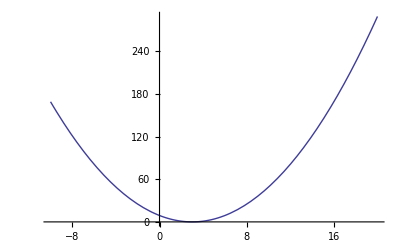

```mathematica
Plot[(x-3)^2,{x,-10,20}]
```

- Tracé superposé des courbes de sin(x), sin(2x),  et sin(3x) pour x variant de 0 à 2π :

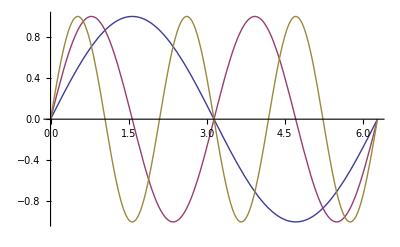

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi}]
```

Consultez la page d'aide de la fonction "Plot" pour voir toutes les options disponibles (on peut changer l'échelle, les couleurs, afficher le nom des axes, etc...).

- Tracé en 3D d'une fonction à deux variables  :

```mathematica
Plot3D[Sin[x ^2+y^2],{x,-3,3},{y,-1,1}]
```

-Graphics3D-

## Exercices

1) Définir la fonction f(x)=x+2+(3x+5)/(x+2)^2.

2) Calculer la dérivée de f(x) par rapport à x. Calculer les zéros de la dérivée. Exprimer la dérivée sous forme factorisée afin de vérifier ses zéros.

3) Calculer les valeurs numériques de f(x) aux zéros de sa dérivée.

4) Calculer la dérivée seconde de f(x) par rapport x. Calculer les valeurs numériques de la dérivée seconde aux zéros de la dérivée première calculés précédemment. Conclure sur la convexité/concavité de f(x).

5) Calculer les limites de f(x)  quand x→-∞,   x→-2   et x→+∞.

6) Calculer le développement limité de f(x)  en x=0 à l'ordre 4. Calculer le développement asymptotique de f(x)  à l'ordre 2 quand x→+∞ et x → -∞. En déduire que la courbe de f(x)  admet une asymptote oblique quand  x→+∞ et  x→ -∞.

7) Tracer la courbe de f(x) ainsi que son asymptote oblique. Ajuster éventuellement l'échelle en ordonnée avec l'option "PlotRange" de la fonction "Plot" (consultez l'aide).

## Solution

1) Définir la fonction f(x)=x+2+(3x+5)/(x+2)^2.

```mathematica
f[x_]:=x+2+(3x+5)/(x+2)^2
```

2) Calculer la dérivée de f(x) par rapport à x. Calculer les zéros de la dérivée. Exprimer la dérivée sous forme factorisée afin de vérifier ses zéros.

```mathematica
f'[x]
```

1+3/(2+x)^2-(2 (5+3 x))/(2+x)^3

```mathematica
Solve[f'[x]==0,x]
```

{{x→-4},{x→-1},{x→-1}}

```mathematica
Factor[f'[x]]
```

((1+x)^2 (4+x))/(2+x)^3

3) Calculer les valeurs numériques de f(x) aux zéros de sa dérivée.

```mathematica
f'[-4]
f[-1]
```

0

3

4) Calculer la dérivée seconde de f(x) par rapport x. Calculer les valeurs numériques de la dérivée seconde aux zéros de la dérivée première calculés précédemment. Conclure sur la convexité/concavité de f(x).

```mathematica
Factor[f''[x]]
```

(6 (1+x))/(2+x)^4

```mathematica
f''[-4]
f''[-1]
```

-9/8

0

5) Calculer les limites de f(x)  quand x→-∞,   x→-2   et x→+∞.

```mathematica
Limit[f[x],x-> -Infinity]
Limit[f[x],x-> -2]
Limit[f[x],x-> Infinity ]
```

-∞

-∞

∞

6) Calculer le développement limité de f(x)  en x=0 à l'ordre 4. Calculer le développement asymptotique de f(x)  à l'ordre 2 quand x→+∞ et x → -∞. En déduire que la courbe de f(x)  admet une asymptote oblique quand  x→+∞ et  x→ -∞.

```mathematica
Series[f[x],{x,0,4}]
```

13/4+x/2+(3 x^2)/16-x^3/16+x^4/64+O[x]^5

```mathematica
Series[f[x],{x,Infinity,2}]
Series[f[x],{x,-Infinity,2}]
```

x+2+3/x-7/x^2+O[1/x]^3

x+2+3/x-7/x^2+O[1/x]^3

7) Tracer la courbe de f(x) ainsi que son asymptote oblique. Ajuster éventuellement l'échelle en ordonnée avec l'option "PlotRange" de la fonction "Plot" (consultez l'aide).

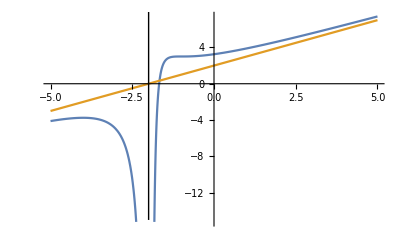

```mathematica
Plot[{f[x],x+2},{x,-5,5},Epilog->Line[{{-2,10},{-2,-15}}]]
```